# Examples for the use of RTNI discussed in the paper

```mathematica
SetDirectory[NotebookDirectory[]];
<<RTNI`
```

Package RTNI (Random Tensor Network Integrator) version 1.0.5 (last modification: 26/01/2019).

Loading precomputed Weingarten Functions from /precomputedWG/functions1.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions2.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions3.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions4.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions5.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions6.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions7.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions8.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions9.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions10.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions11.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions12.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions13.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions14.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions15.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions16.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions17.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions18.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions19.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions20.txt

# Example: Creation of Figure 3 in main paper

{{U,1,out,1},{U,2,out,1}}

{{U,1,in,1},{A,1,out,1}}

{{U,2,in,1},{A,1,out,2}}

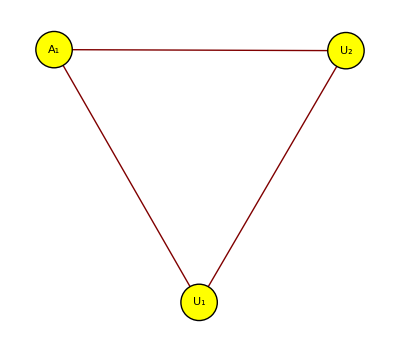

visualizeTNnoedgelabels.pdf

-Graphics-

visualizeTNedgelabels.pdf

```mathematica
e1={{"U",1,"out",1},{"U",2,"out",1}}
e2={{"U",1,"in",1},{"A",1,"out",1}}
e3={{"U",2,"in",1},{"A",1,"out",2}}
g={e1,e2,e3};
visualizeTN[g]
Export["visualizeTNnoedgelabels.pdf",%]
visualizeTN[g,{EdgeLabeling->True}]
Export["visualizeTNedgelabels.pdf",%]
```

# Example 6.1: Twirling a matrix

{{{U,1,out,1},{X,1,in,1}},{{Y,1,out,1},{U,1,in,1}},{{U*,1,out,1},{Y,1,in,1}},{{X,1,out,1},{U*,1,in,1}}}

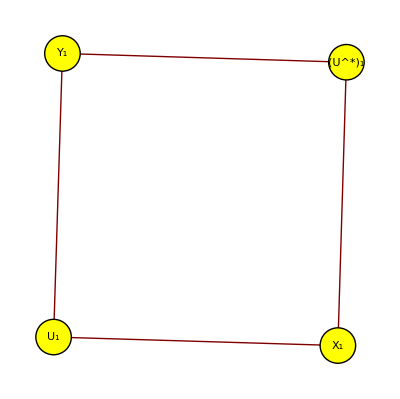

TrXUYUstar.pdf

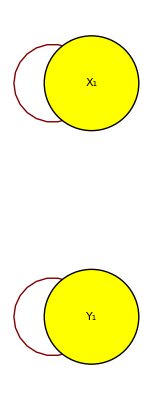
{{-Graphics-,1/d}}

ETrXUYUstar.pdf

```mathematica
e1={{"U",1,"out",1},{"X",1,"in",1}};
e2={{"Y",1,"out",1},{"U",1,"in",1}};
e3={{"U*",1,"out",1},{"Y",1,"in",1}};
e4={{"X",1,"out",1},{"U*",1,"in",1}};
g={e1,e2,e3,e4}
visualizeTN[g]
(* alternative: visualizeTN[{{g,1}},{EdgeLabeling->True}]*)
Export["TrXUYUstar.pdf",%]
Eg=integrateHaarUnitary[g,"U",{d},{d},d];
visualizeTN[Eg]
Export["ETrXUYUstar.pdf",%]
```

{{{U,1,out,1},{X,1,in,1}},{{Y,1,out,1},{U,1,in,1}},{{U*,1,out,1},{Y,1,in,1}}}

{{{{{Y,1,out,1},{Y,1,in,1}},{{X,1,in,1},{dummy-U*-IN-1-1,1,out,1}}},1/d}}

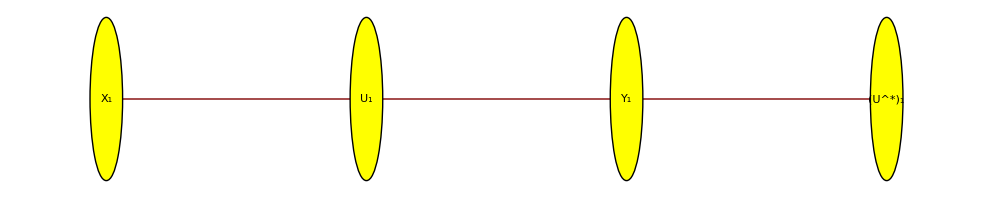

XUYUstar.pdf

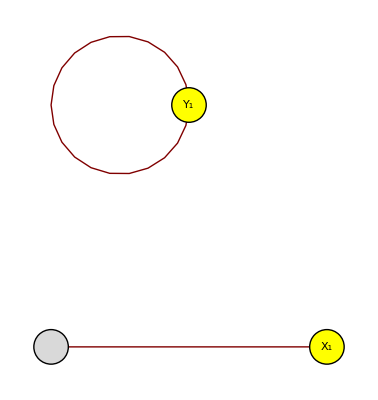
{{-Graphics-,1/d}}

EXUYUstar.pdf

```mathematica
e1={{"U",1,"out",1},{"X",1,"in",1}};
e2={{"Y",1,"out",1},{"U",1,"in",1}};
e3={{"U*",1,"out",1},{"Y",1,"in",1}};
g={e1,e2,e3}
Eg=integrateHaarUnitary[g,"U",{d},{d},d]
visualizeTN[g]
Export["XUYUstar.pdf",%]
visualizeTN[Eg]
Export["EXUYUstar.pdf",%]
```

# Example 6.2: Several tensor factors

{{{A,1,out,1},{U,1,in,1}},{{A,1,out,2},{U,1,in,2}},{{U*,1,out,1},{A,1,in,1}},{{U*,1,out,2},{A,1,in,2}},{{U,1,out,2},{U*,1,in,2}}}

{{{{{A,1,out,1},{A,1,in,1}},{{A,1,out,2},{A,1,in,2}},{{dummy-U-OUT-1-1,1,in,1},{dummy-U*-IN-1-1,1,out,1}}},1/n}}

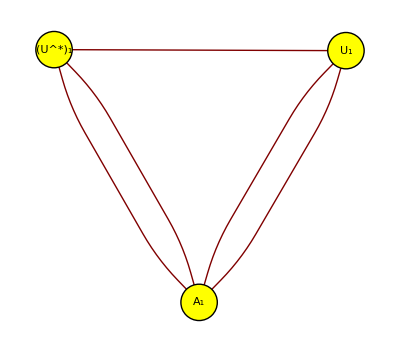

id-Tr-UU-A-UstarUstar.pdf

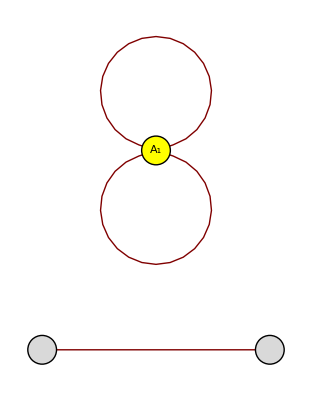
{{-Graphics-,1/n}}

E-id-Tr-UU-A-UstarUstar.pdf

```mathematica
e1={{"A",1,"out",1},{"U",1,"in",1}};
e2={{"A",1,"out",2},{"U",1,"in",2}};
e3={{"U*",1,"out",1},{"A",1,"in",1}};
e4={{"U*",1,"out",2},{"A",1,"in",2}};
e5={{"U",1,"out",2}, {"U*",1,"in",2}};
g={e1,e2,e3,e4,e5}
Eg=integrateHaarUnitary[g,"U",{n,k},{n,k},n k]
visualizeTN[g]
Export["id-Tr-UU-A-UstarUstar.pdf",%]
visualizeTN[Eg]
Export["E-id-Tr-UU-A-UstarUstar.pdf",%]
```

# Example 6.3: Bi-partite twirling

{{{X,1,out,1},{U,1,in,1}},{{U*,1,out,1},{X,1,in,1}},{{X,1,out,2},{U,2,in,1}},{{U*,2,out,1},{X,1,in,2}}}

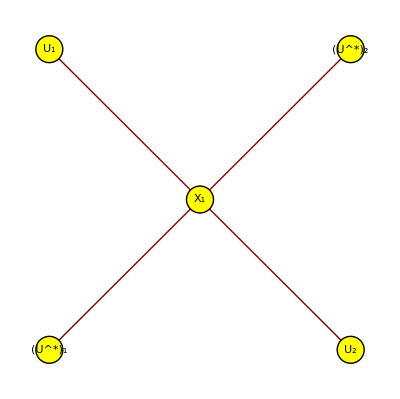

twirl.pdf

{{{{{X,1,out,1},{X,1,in,1}},{{X,1,out,2},{X,1,in,2}},{{dummy-U-OUT-1-1,1,in,1},{dummy-U*-IN-1-1,1,out,1}},{{dummy-U-OUT-2-1,1,in,1},{dummy-U*-IN-2-1,1,out,1}}},1/(-1+d^2)},{{{{X,1,out,1},{X,1,in,1}},{{X,1,out,2},{X,1,in,2}},{{dummy-U-OUT-1-1,1,in,1},{dummy-U*-IN-2-1,1,out,1}},{{dummy-U-OUT-2-1,1,in,1},{dummy-U*-IN-1-1,1,out,1}}},1/(d-d^3)},{{{{X,1,out,1},{X,1,in,2}},{{X,1,out,2},{X,1,in,1}},{{dummy-U-OUT-1-1,1,in,1},{dummy-U*-IN-1-1,1,out,1}},{{dummy-U-OUT-2-1,1,in,1},{dummy-U*-IN-2-1,1,out,1}}},1/(d-d^3)},{{{{X,1,out,1},{X,1,in,2}},{{X,1,out,2},{X,1,in,1}},{{dummy-U-OUT-1-1,1,in,1},{dummy-U*-IN-2-1,1,out,1}},{{dummy-U-OUT-2-1,1,in,1},{dummy-U*-IN-1-1,1,out,1}}},1/(-1+d^2)}}

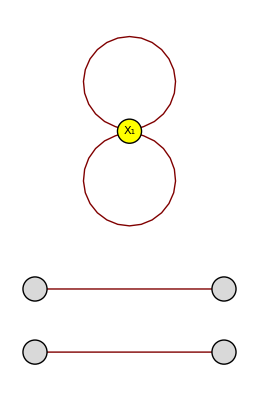
{{-Graphics-,1/(-1+d^2)},{-Graphics-,1/(d-d^3)},{-Graphics-,1/(d-d^3)},{-Graphics-,1/(-1+d^2)}}

E-twirl.pdf

```mathematica
e1={{"X",1,"out",1},{"U",1,"in",1}};
e2={{"U*",1,"out",1},{"X",1,"in",1}};
e3={{"X",1,"out",2},{"U",2,"in",1}};
e4={{"U*",2,"out",1},{"X",1,"in",2}};
g={e1,e2,e3,e4}
visualizeTN[g]
Export["twirl.pdf",%]
integrateHaarUnitary[g,"U",{d},{d},d]
visualizeTN[%,EdgeLabeling->True]
Export["E-twirl.pdf",%]
```

# Example 6.4: Bell state as input in conjugate random quantum channels

```mathematica
e1={{"U*",2,"out",1},{"U",1,"in",1}};
e2={{"U*",1,"out",1},{"U",2,"in",1}};
e3={{"U",1,"out",1},{"U*",1,"in",1}};
e4={{"U",2,"out",1},{"U*",2,"in",1}};
e5={{"U",1,"out",2},{"U*",2,"in",2}};
e6={{"U",2,"out",2},{"U*",1,"in",2}};
g={e1,e2,e3,e4,e5,e6};
listg={{g,1/(d k)}};
Eg=integrateHaarUnitary[listg,"U",{d},{n,k},n k]
overlap=Eg[[1,2]];
overlapt=overlap/.{d->t n k};
Assuming[t>0&&k>1,Limit[overlapt,n->Infinity]]//Simplify
```

{{{},-(d^2 k^2 n)/(d k-d k^3 n^2)-(d k n^2)/(d k-d k^3 n^2)+(d k^2 n)/(d k^2 n-d k^4 n^3)+(d^2 k n^2)/(d k^2 n-d k^4 n^3)}}

(1-t)/k^2+t

# Example 6.5: Random tensor networks for holographic duality

```mathematica
(* see separate file examples_holographictensornetworks*)
```

# Example 6.6: Computation of expectation values of matrix products

```mathematica
MultinomialexpectationvalueHaar[d,{1,2},{X,Y},False]
```

(X Tr[Y])/d

```mathematica
MultinomialexpectationvalueHaar[d,{1,3},{X,Y},False]
```

0

```mathematica
MultinomialexpectationvalueHaar[d,{2,3},{X,Y},False]
```

(X.Transpose[Y])/d

```mathematica
MultinomialexpectationvalueHaar[d,{1,4},{X,Y},True]
```

Tr[X.Transpose[Y]]/d

```mathematica
MultinomialexpectationvalueHaar[d,{1,2,3,4},{V,W,X,Y},False]
```

(V.Transpose[Y].X.Transpose[W])/(-1+d^2)+(V.Transpose[Y].X Tr[W])/(d-d^3)+(V.X.Transpose[W] Tr[Y])/(d-d^3)+(V.X Tr[W] Tr[Y])/(-1+d^2)

```mathematica
(* for additional examples for the use of MultinomialexpectationvalueHaar, see file examples_momentcalculator.nb*)
```